# Concentration dependence of bimolecular reactions

## Bimolecular, concentration-dependent reactions

#### G. Woehlke, Aug. 2025

## Kinetic Scheme

Given is the following system, in which one molecule flips between two conformations:
   A + B ⇌ C 
This might describe a protein that binds a ligand, e.g. myoglobin and O_2 or similar (important: only one ligand binding site, no cooperative effects as in hemoglobin). Concentrations A, B and C will change with velocities x(t), y(t), and z(t):

## Graph of Temporal Development of Concentrations A, B, and C

Time trace of concentrations   A + B ⇌ C

In case variables are predefined in other notebooks:

```mathematica
Unset[{t,x,y,z,x[0],y[0],z[0],x[t],y[t],z[t],x'[t],y'[t],z'[t],k12,k21,zeitachse}];
```

Unset::norep: Assignment on x for x[0] not found.

Unset::norep: Assignment on y for y[0] not found.

Unset::norep: Assignment on z for z[0] not found.

General::stop: Further output of Unset::norep will be suppressed during this calculation.

```mathematica
Manipulate[
Plot[
{Evaluate[x[t]/.NDSolve[
{k12==(k21 z[t]+z'[t])/(x[t] y[t]),x[0]==1,y[0]==cy,z[0]==0,x'[t]==y'[t],-x'[t]==z'[t]},{x[t],y[t],z[t]},{t,0,10}
][[1]][[1]]],
Evaluate[z[t]/.NDSolve[
{k12==(k21 z[t]+z'[t])/(x[t] y[t]),x[0]==1,y[0]==cy,z[0]==0,x'[t]==y'[t],-x'[t]==z'[t]},{x[t],y[t],z[t]},{t,0,10}
][[1]][[3]]],
(-1+1 k12/k21-cy k12/k21+√(4 1 k12/k21+(-1+1 k12/k21-cy k12/k21)^2))/(2 k12/k21),(-1+(2+1-cy) k12/k21+√(4 1 k12/k21+(1-1 k12/k21+cy k12/k21)^2))/(4 k12/k21)},
{t,0,zeitachse},
PlotRange->{{0,zeitachse},{0,1.04}},
PlotLabel->"Bimolecular reaction A + B ⇌ C",
PlotStyle->{{Blue,Thickness[thn]},{RGBColor[0.65,0.65,1],Thickness[thn]},{Gray,Dashed},{Gray,Dashed}},
AxesLabel->{"time/s","concentration\r(over time)"},
LabelStyle->Directive[FontFamily->Arial,Bold,fs],
ImageSize->is,
Epilog->{Inset[Style[StringJoin[{"c_B(0) = ",ToString[cy]," M",
"\rk_12 =   ",ToString[k12]," M^-1s^-1",
 "\rk_21 =   ",ToString[k21]," s^-1",
 "\rK_D =   ",ToString[k21/k12]," M"}],{FontFamily->Arial,Bold,fs},TextAlignment->Left],{0.8 zeitachse,0.9}]}],
{{is,720,"Image Size"},{450,650,720,900,1080}},
{{thn,0.005,"Line Thickness"},{0.002,0.0035,0.005,0.0067,0.008,0.01}},
{{fs,14,"Font Size"},{9,12,14,18,24}},
{{k12,10.,"k_12"},0.01,25,0.5,Appearance->"Open"},
{{k21, 1.,"k_21"},0.01,25,0.5,Appearance->"Open"},
{{cy,1.,"initial conc' B"},0.01,10.,0.1,Appearance->"Open"},
{{zeitachse, 0.8,"time axis"},0.2,5,0.1}]
```

Figure legend: Numerical simulation of the bimolecular association of A and B using NDSolve[ ]. Initial values are c_A(0) = 1., c_C(0) = 0, rates k_12 and k_21, as well as c_B(0) may be varied. The lower horizontal line indicates the equilibrium concentration of A, the line above shows the level of half of the substrate turnover.

Side calculations for the y-position of horizontal lines:

```mathematica
Solve[(cA0-cAeq)/(cAeq (cB0-(cA0-cAeq)))==K,cAeq]
```

{{cAeq→(-1+cA0 K-cB0 K+√(4 cA0 K+(-1+cA0 K-cB0 K)^2))/(2 K)},{cAeq→-(1-cA0 K+cB0 K+√(4 cA0 K+(-1+cA0 K-cB0 K)^2))/(2 K)}}

```mathematica
FullSimplify[(1-((-1+cA0 K-cB0 K+√(4 cA0 K+(-1+cA0 K-cB0 K)^2))/(2 K)))/2+(-1+cA0 K-cB0 K+√(4 cA0 K+(-1+cA0 K-cB0 K)^2))/(2 K)]
```

(-1+(2+cA0-cB0) K+√(4 cA0 K+(1-cA0 K+cB0 K)^2))/(4 K)

```mathematica
FullSimplify[(-1+cA0 K-cB0 K+√(4 cA0 K+(-1+cA0 K-cB0 K)^2))/(2 K)]
```

(-1+cA0 K-cB0 K+√(4 cA0 K+(1-cA0 K+cB0 K)^2))/(2 K)

A table of half-life times in dependence of the initial concentration of B may be read from the graph above. The rates are Log[2.] × the inverse of these half-life times, and follow the concentration dependence below:

```mathematica
data=Thread[{{.1,.2,.3,.4,.5,.75,1.,1.5,2.,2.5,3.,4.,5.,7.5,10.},{Log[2.]/0.065,Log[2.]/0.065,Log[2.]/0.066,Log[2.]/0.066,Log[2.]/0.067,Log[2.]/0.064,Log[2.]/0.0605,Log[2.]/0.047,Log[2.]/0.036,Log[2.]/0.029,Log[2.]/0.024,Log[2.]/0.018,Log[2.]/0.014,Log[2.]/0.00952,Log[2.]/0.00717}}];
```

```mathematica
data//TableForm
```

0.1 | 10.6638
0.2 | 10.6638
0.3 | 10.5022
0.4 | 10.5022
0.5 | 10.3455
0.75 | 10.8304
1. | 11.457
1.5 | 14.7478
2. | 19.2541
2.5 | 23.9016
3. | 28.8811
4. | 38.5082
5. | 49.5105
7.5 | 72.8096
10. | 96.6732

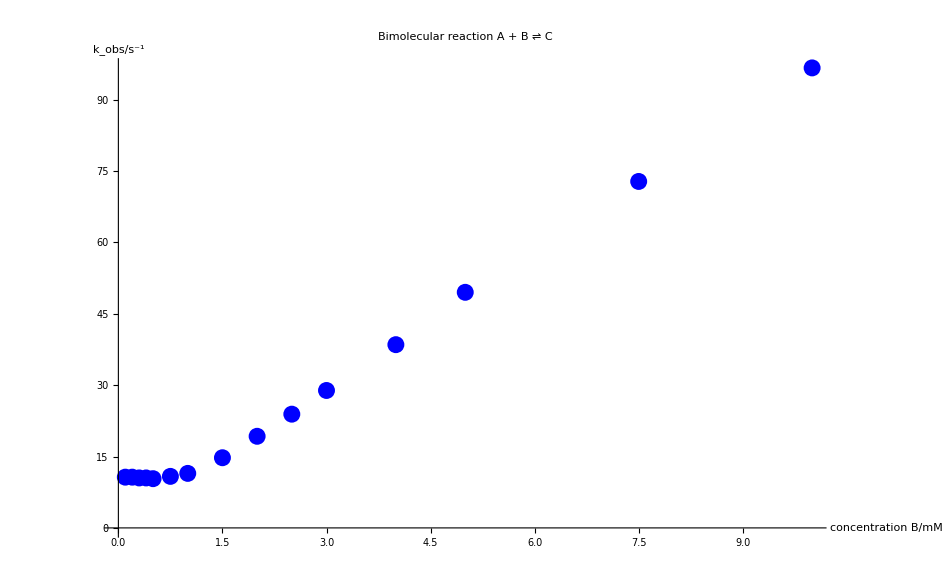

```mathematica
ListPlot[data,
PlotLabel->"Bimolecular reaction A + B ⇌ C",
PlotStyle->{{Blue,Thickness[0.0067]},{RGBColor[0.65,0.65,1],Thickness[0.005]}},
AxesLabel->{"concentration B/mM","k_obs/s^-1"},
LabelStyle->Directive[FontFamily->Arial,Bold,14],
ImageSize->950]
```

Figure legend: Concentration dependence of the bimolecular association reaction A + B ⇌ C 
The initial concentration of A is fixed at 1, the forward rate is k_12=10., the backward rate k_21=0.1. The rates are read out from figure [X], and show a linear dependence as soon as the (substrate) concentration of B exceeds the (enzyme) concentration of A. The slope from 2 mM to 10 mm is (139.5 - 27.8)/8 = 13.96 M^-1 s^-1.

```mathematica
line = Fit[data[[8;;15]], {1,c},c]
```

0.00469525+9.69714 c

The linear fit of our data from the 8th to the last concentration results in an apparent bimolecular rate constant of 9.7 × M^-1 s^-1, and a zero intercept @ 0 s^-1.

## Comparison to Python Code

Python code: 
#!/usr/local/bin/python3
import matplotlib.pyplot as plt
import numpy as np
concreihe=[0.65,0.7,0.8,0.9,1.,1.1,1.2]
rates=[1/0.327,1/0.239,1/0.163,1/0.132,1/0.111,1/0.095,1/0.082]
plt.xlabel(‘concentration B’)
plt.ylabel(‘rate’)
plt.title(“Numerical Model of Bimolecular Reaction 06.08.2025”)
plt.legend()
plt.plot(concreihe,rates,’o’)
plt.show()
-Graphics-